#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

Experimental results for the total cross section for deuteron photodisintegration
(W. Jaus & W.S. Woolcock -- Nuclear Physics A473 (1987) 685-704)
[σ_tot]=μb=10^-4 fm^2
[Lab photon energy] = MeV

```mathematica
DeutDataMuBarn=ReadList["../../../data/deuteron_diss_tot_exp.dat",Number,RecordLists->True];
DeutDataFm2=Transpose[{Transpose[DeutData][[1]],Transpose[DeutData][[2]] 10.^(-4)}];
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
hat[l_]:=Sqrt[2 l+1];
SetDirectory["/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0,1,2};
J0=1;
mIns=Range[-#,#,1]&/@Subscript[I, n];

thresholdLIT=10^(-9);
thresholdD=thresholdLIT;
mom=ReadList["kRange.dat",Number][[2]];
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
```

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,0.2];
```

min/max: {9.23385×10^-6,7.14103}

(min/max) discarded elements: 18 {9.23385×10^-6,0.114133}

#### The real calculation

Set a sensible cut-off

min/max: {9.23385×10^-6,7.14103}

(min/max) discarded elements: 0 {∞,-∞}

B(D) = -2.24018

Dim_full^deuteron = 32=^!32   ;     Dim_(non - singular)^deuteron = 32

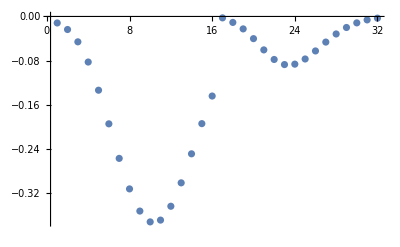

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[DNmhi].DHam.DNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(D) = ",e0];
Print["Dim_full^deuteron = ",Dimensions[DNorm][[1]],"=^!",DBasisDim,"   ;     Dim_(non - singular)^deuteron = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[DNmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = {46,46,46}

min/max: {4.27931×10^-16,15.3699}

(min/max) discarded elements: 15 {4.27931×10^-16,5.48756×10^-10}

J=0:  E_0=0.0882611

min/max: {3.75402×10^-16,15.3699}

(min/max) discarded elements: 15 {3.75402×10^-16,5.48757×10^-10}

J=1:  E_0=0.0882767

min/max: {3.45367×10^-16,15.3699}

(min/max) discarded elements: 15 {3.45367×10^-16,5.48756×10^-10}

J=2:  E_0=0.0882676

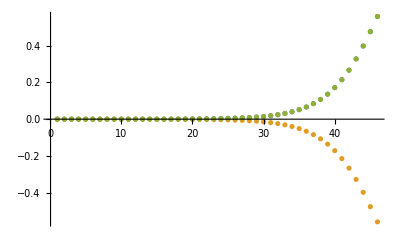

```mathematica
LitNmhis={};
fullv0l={};
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Normalize[Transpose[LitNmh].v0l]];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_S_*"],"_"][[All,1]]]];
ks=Range[0,nk];


CouplingBlockj={};
Do[
CouplingBlock={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

CouplingBlocks={};
Do[
files="./"<>ToString[#]<>"_S_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_"<>ToString[mL]<>".lit"&/@ks;
(*Print[files];*)
inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[DBasisDim+1;;,;;DBasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["Cell["⟨",ExpressionUUID->"0d6cc698-9e19-4819-a044-69e9596ebc5c"]",multipolarity,mL,J0,mIn-mL,"Cell["|",ExpressionUUID->"7022f64c-53bc-4f2e-a22d-2ebd29c38e98"]",Subscript[I, n][[nj]],mIn,"Cell["⟩",ExpressionUUID->"5c883ae8-1c11-4fe8-84e5-4c599a958f61"] =  ",coupl];
Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]];
,{mL,mM}
]

AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
(*Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]//MatrixForm];*)
,{mIn,mIns[[nj]]}]

AppendTo[CouplingBlockj,CouplingBlock];
,{nj,Range[1,Length[Subscript[I, n]]]}]

Print["Dim(⟨ψ|ο̂|deuteron⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|deuteron⟩) = {3,46,32}

Dim(⟨ψ|Ĥ|ψ⟩) = {3,46,46}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {3,46,46}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=4.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],#[[1]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λsLit,trfLit,inhomo,egs,evgs},
OμRHS=normreg[thresholdD,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thresholdLIT,LITNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

(*Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];*)

inhomo=(2/mom) (Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λsLit,(trfLit.inhomo)^2,egs}
];
Clear[litcomp];
litcomp[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:=Block[{λscf=decompose[thresholdD,thresholdLIT,DNorm,DHam,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/((#[[1]]-egrnd-σRe)^2+σI^2))&/@tmpp)];
```

```mathematica
Clear[LIT,LITs,testfu];

minth=thresholdLIT;maxth=.02 thresholdLIT;nth=1;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

LITsj={};

Do[
testfu={};
Print["I_n=",Subscript[I, n][[nj]]];
Do[

tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[testfu,Evaluate[litcomp[#,#,DNorm,DHam,LitNorm[[nj]],LitHam[[nj]],tmp]&/@thresholdrng]];

,{mm,Length[mIns[[nj]]]}
];

AppendTo[LITsj,(*(-1)^(Subscript[I, n][[nj]]-J0)*) Total[testfu]/.σRe->σRs];
,{nj,Range[1,Length[Subscript[I, n]]]}
]

thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);

plote=ListPlot[Flatten[(Transpose[{σRs,#}]&/@LITsj[[#]])&/@Range[1,Length[Subscript[I, n]]],1],
PlotLabel->Style["σ_I = "<>ToString[σI]<>"    ; J_lit = "<>ToString[Subscript[I, n]],18,Red],
AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},
PlotLegends->Placed[thrlegend,Above],
LabelStyle->12,ImageSize->ImgSize,PlotRange->Full,
Mesh->5,MeshFunctions->{#2&,#2&,#2&},PlotMarkers->{Automatic,Scaled[0.01 #]}&/@Range[1,nth],
Joined->True];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

I_n=0

I_n=1

I_n=2

plot.pdf

E_0( th=1.×10^-9 ) = -2.24018    dim(D,LIT) = {32}{31}

E_0( th=1.×10^-9 ) = -2.24018    dim(D,LIT) = {32}{31}

E_0( th=1.×10^-9 ) = -2.24018    dim(D,LIT) = {32}{31}

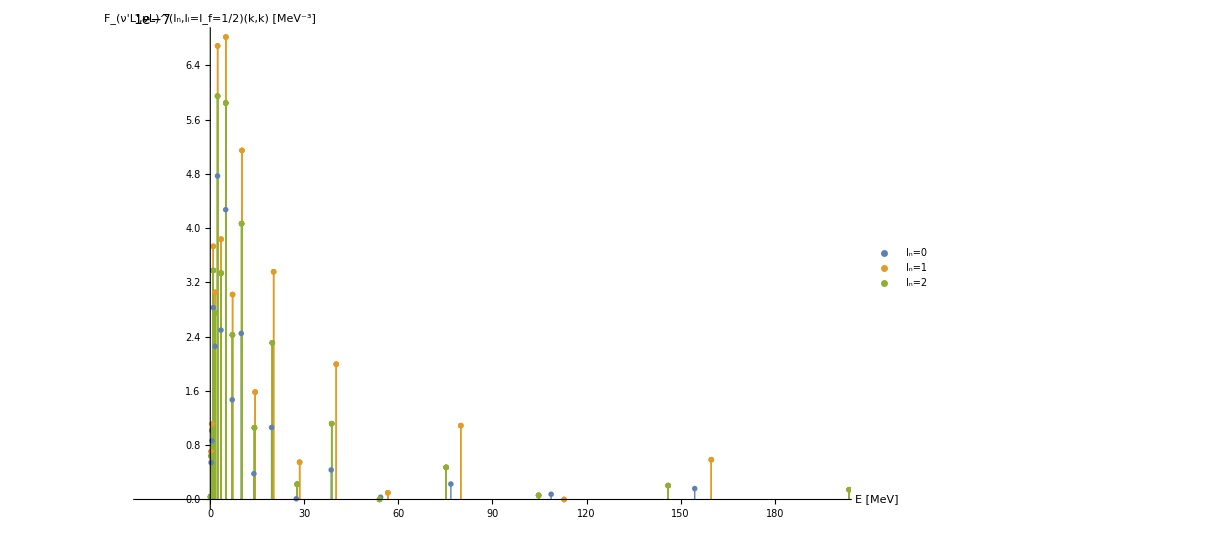

```mathematica
Clear[thresh,es,μ,transf];
lpsis={};
thresh=thresholdD;

es=Eigensystem[DNorm];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresh&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];
leg={};
Do[
lpsi={};
esl=Eigensystem[LitNorm[[nj]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresh&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam[[nj]]).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];

Do[
inhomo=(2/mom) (Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
AppendTo[lpsi,Transpose[{λsLit,(trfLit.inhomo)^2}]];

,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Flatten[lpsi,1]];
AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

,{nj,Range[1,Length[Subscript[I, n]]]}
]

ListPlot[lpsis,Joined->False,PlotMarkers->{{♪,12},{♔,12}},Filling->Axis,FillingStyle->{{Blue},{Green}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["F_(ν'L',νL)^(I_n,I_i=I_f=1/2)(k,k) [MeV^-3]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
StrengthFLorentz[E_,eps_,psiSQ_,lamM_]:=Pi^-1 psiSQ eps/((E-lamM)^2+eps^2);
StrengthFLorentzTH[E_,eps_,psiSQ_,lamM_,E0_]:=(2 eps/(Pi+2 ArcTan[(lamM-E0)/eps]))  psiSQ/((E-lamM)^2+eps^2);
StrengthFGauss[E_,eps_,psiSQ_,lamM_]:= psiSQ Exp[-(E-lamM)^2/(4 eps)]/(2 Sqrt[eps Pi]);
StrengthFGaussTH[E_,eps_,psiSQ_,lamM_,E0_]:= psiSQ Exp[-(E-lamM)^2/(4 eps)]/(Sqrt[eps Pi] (1+Erf[(lamM-E0)/Sqrt[4 eps]])) HeavisideTheta[E-E0];
StrengthFSinc[E_,eps_,psiSQ_,lamM_]:=(Pi (E-lamM))^-1 psiSQ Sin[(E-lamM)/eps];
StrengthFBessel[E_,eps_,psiSQ_,lamM_]:= psiSQ BesselJ[1/eps,(E-lamM+1)/eps]/eps;
StrengthFLaguerre[E_,eps_,psiSQ_,lamM_,nn_]:= psiSQ/Sqrt[Pi eps] Abs[Exp[-eps^-1 (E-lamM)^2]LaguerreL[nn,2 (E-lamM)/eps]];
```

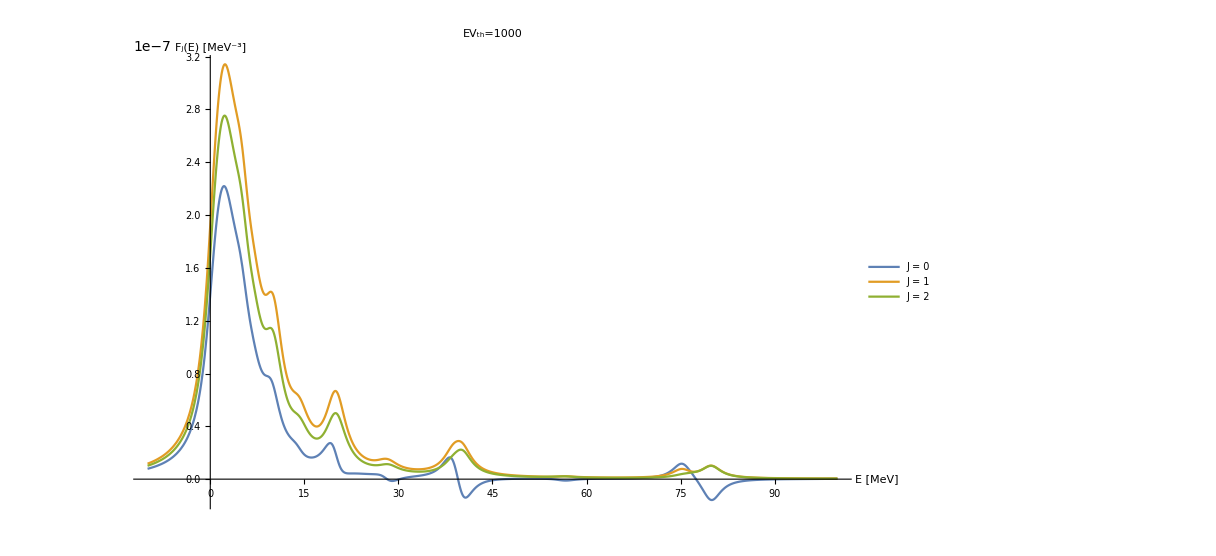

```mathematica
responseListJ={};

evth=10^3;
epsi=1.9;
jJtot={0,1,2};
Do[
responseListI={};
Do[
response=Total[SixJSymbol[{1,1,jJtot[[nj]]},{1,1,Subscript[I, n][[nIn]]}] StrengthFLorentz[e2,epsi,#[[2]],#[[1]]]&/@Select[lpsis[[nIn]],#[[1]]<evth&]];
AppendTo[responseListI,response];
,{nIn,Range[1,Length[Subscript[I, n]]]}
];
AppendTo[responseListJ,Total[responseListI]];
,{nj,Range[1,Length[jJtot]]}
];



labeljlit=("J = "<>ToString[#])&/@jJtot;

Plot[responseListJ,{e2,-10,100},PlotRange->{{-10,100},Full},PlotLegends->Placed[labeljlit,Bottom],AxesLabel->{"E [MeV]","F_j(E) [MeV^-3]"},PlotLabel->"EV_th="<>ToString[evth],LabelStyle->Directive[Larger],ImageSize->ImgSize]
```

#### real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

#### imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii) fm^2=10^-2 b=10mb
iv) σ(M^ν L)=(-)^(L+1)(4π)/(√(2 J_i+1)·√(2 L+1)k) ImP_0 
      from eq.(4.38) “H. Arenhoevel -- SUBNUCLEAR DEGREES OF FREEDOM IN PHOTOABSORPTION AND SCATTERING in new vistas...

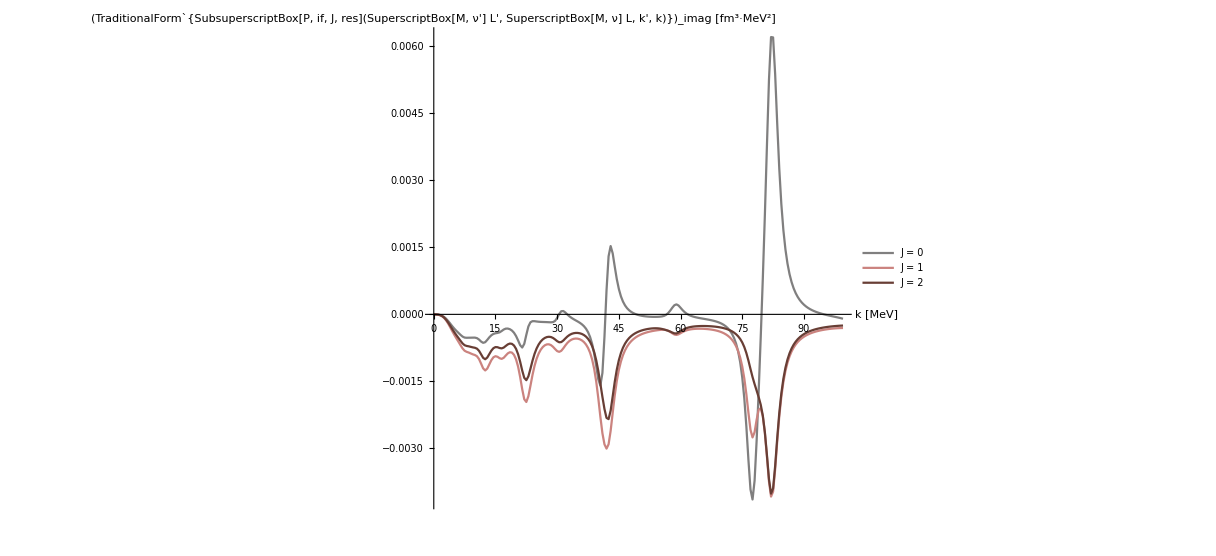

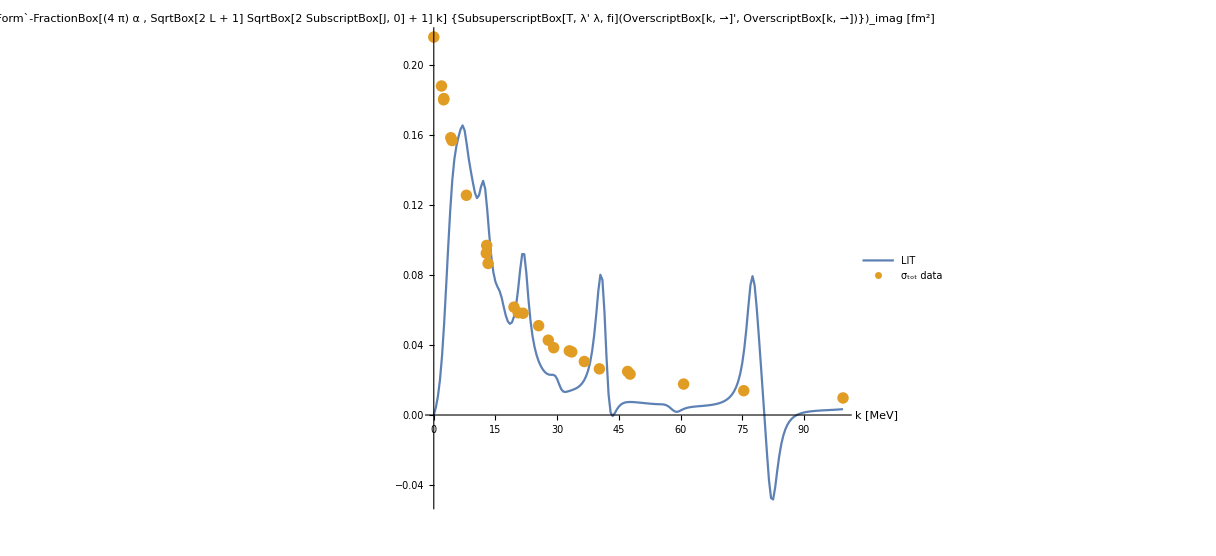

```mathematica
Clear[ee,e2];
k0=0.001;k1=100;dK=0.5;
kσ=Range[k0,k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;
Jj=jJtot;
labelj=("J = "<>ToString[#])&/@Jj;
strengthfunctionList=Table[Table[((ee-e0)^2 responseListJ[[nJ]]/.e2->ee)/.ee->(e0+kmag),{kmag,kσ}],{nJ,Range[1,Length[jJtot]]}];

ImPList=2 Pi^2 (-1)^(multipolarity+Jf+Ji) hat[multipolarity] hat[multipolarity] strengthfunctionList;
z=List[];

For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];
Show[z,PlotRange->All]

ImT[Mf_,Mi_,λf_,λi_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,(
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{multipolarity,Mm},{multipolarity,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{multipolarity,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(1)^(1+λf+Jf-Mi)*ampli]
]
kinfac=(-1)^(multipolarity+1)(6 2 Pi hbarc^2)/(√(2 J0+1) √(2 multipolarity+1) kσ 137);

DissCross[Mf_,Mi_,λf_,λi_,θ_,kinfac_]:=kinfac ImT[Mf,Mi,λf,λi,θ];
ListPlot[{Re[DissCross[Jf,Ji,0,0,0,kinfac]],DeutDataFm2},PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`-FractionBox[(4  π) α , SqrtBox[2  L + 1] SqrtBox[2 SubscriptBox[J, 0] + 1] k] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [fm^2]"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[kσ],Max[kσ]},PlotLegends->{"LIT","σ_tot data"}]
```